# Domača naloga – Mathematica

## 1. naloga

1. Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. Rešite neenačbo:|x-1|≤ 2x+3 
3. Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.
4. S funkcijo FindRoot numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
∑_(k=1)^30 k^2/(k+5)
```

189870299151349/525103828704

```mathematica
Reduce[Abs[x-1]<=2x+3]
```

x≥-2/3

```mathematica
f[x_]:=3*Tan[2*Cos[x]+1]*Sin[x]
```

```mathematica
f'[x]
```

-6 Sec[1+2 Cos[x]]^2 Sin[x]^2+3 Cos[x] Tan[1+2 Cos[x]]

```mathematica
Simplify[-6 Sec[1+2 Cos[x]]^2 Sin[x]^2+3 Cos[x] Tan[1+2 Cos[x]]]
```

-6 Sec[1+2 Cos[x]]^2 Sin[x]^2+3 Cos[x] Tan[1+2 Cos[x]]

```mathematica
x/.FindRoot[Cos[x]/(ⅇ^x^3-1)==0,{x,1}]
```

1.5708

```mathematica
Clear[x]
```

## 2. naloga

1. Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. Narišite parametrično podano krivuljo na območju t ∈[0,2π].

```mathematica
x[t_]:=Cos[5t]
```

```mathematica
y[t_]:=0.5*Sin[t]
```

```mathematica
NSolve[Cos[5 t]==0&&0<=t<=π]
```

{{t→0.314159},{t→0.942478},{t→1.5708},{t→2.19911},{t→2.82743}}

```mathematica
k[t_]:={Cos[5t],0.5*Sin[t]}
```

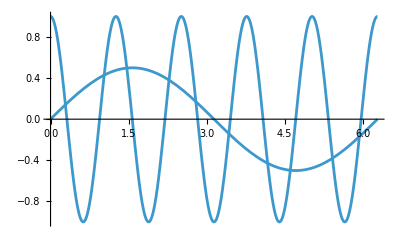

SetDelayed::write: Tag Integer in 1[t_] is Protected.

```mathematica
Plot[k[t],{t,0,2*π}]
```